```mathematica
u=Exp[x] Sin[y]
Plot3D[u,{x,-2,2},{y,-2,2}]
```

ⅇ^x Sin[y]

-Graphics3D-

{ⅇ^x Sin[y],ⅇ^x Cos[y]}

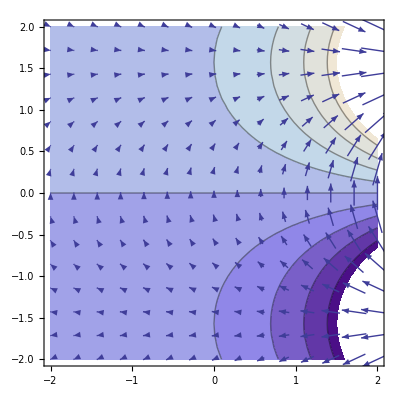

```mathematica
uG={D[u,x],D[u,y]}
Show[
g1=ContourPlot[u,{x,-2,2},{y,-2,2}],
g2=VectorPlot[uG,{x,-2,2},{y,-2,2}]
]
```

```mathematica
uG[[2]]/uG[[1]]/.y->B
Slope=%/.B->y[x]
```

Cot[B]

Cot[y[x]]

```mathematica
(* since the field vector is givn by Gradian
therefore, the slope of the steamline can be found*)
K=y[x]/.DSolve[y'[x]==Slope,y[x],x]//Simplify
```

{-ArcCos[ⅇ^(-x-C[1])],ArcCos[ⅇ^(-x-C[1])]}

```mathematica
F=C[1]/.Solve[y==K[[2]],C[1]]
```

{-x-Log[Cos[y]]}

```mathematica
Exp[-F[[1]]]
```

ⅇ^x Cos[y]

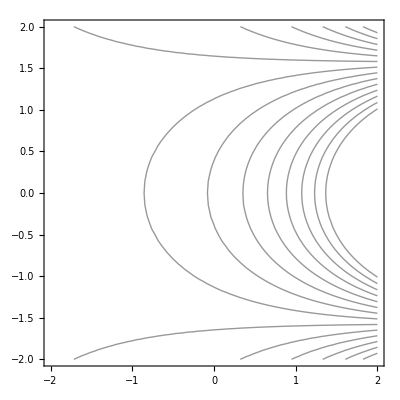

```mathematica
g3=ContourPlot[Exp[x]Cos[y],{x,-2,2},{y,-2,2},AspectRatio->1,ContourShading->None,Contours->Function[{min,max},Range[min,max,0.5]]]
```

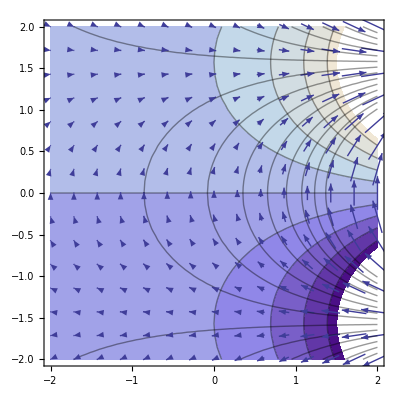

```mathematica
Show[
g1,g2,g3
]
```

```mathematica
D[ⅇ^x Sin[y[x]]==B,x]
```

ⅇ^x Sin[y[x]]+ⅇ^x Cos[y[x]] y'[x]==0

```mathematica
Solve[%,y'[x]]
```

{{y'[x]→-Tan[y[x]]}}

```mathematica
DSolve[y'[x]==-Tan[y[x]],y[x],x]
```

{{y[x]→ArcSin[ⅇ^(-x+C[1])]}}

```mathematica
(* The new y'[x] is perpendicular to the old one, so, *)
DSolve[y'[x]==1/Tan[y[x]],y[x],x]
```

{{y[x]→-ArcCos[ⅇ^(-x-C[1])]},{y[x]→ArcCos[ⅇ^(-x-C[1])]}}